```mathematica
m1:=-1
m2:=2
s12:=1
s22:=4
Expand[8*((x-m1)^2/(2*s12)-(x-m2)^2/(2*s22))/3]
```

4 x+x^2

```mathematica
F[d_]:=NIntegrate[1/Sqrt[2*Pi]*Exp[-t^2/2],{t,-1-d,-1+d}]
```

```mathematica
FindRoot[F[d]-0.9,{d,0}]
```

NIntegrate::nlim: t = -1. - 1.\ d is not a valid limit of integration.

{d→2.28447}

```mathematica
F[2.28]
```

0.899208

```mathematica
x1=-2-2.284468012168643
x2=-1+2.284468012168643
```

-4.28447

1.28447

```mathematica
d
```

d

```mathematica
d=2.284468012168643
```

2.28447

```mathematica
NIntegrate[1/Sqrt[2*Pi*s22]*Exp[-1/(2*s22)*(x-m2)^2],{x,x1,x2}]
```

0.359421

```mathematica
NIntegrate[1/Sqrt[2*Pi*4]*Exp[-1/2/4*(x-2)^2],{x,-2-d,-2+d}]
```

0.194673

```mathematica
NIntegrate[1/Sqrt[2*Pi]*Exp[-1/2*(x)^2],{x,-2-d/2,-2+d/2}]
```

0.194673

```mathematica
fN[t_]:=1/Sqrt[2*Pi]*Exp[-t^2/2]
```

```mathematica
A[d_]:=1-NIntegrate[fN[t],{t,-1-d,-1+d}]
```

SetDelayed::write: Tag Beta in Beta[d_] is Protected.

```mathematica
B[d_]:=NIntegrate[fN[t],{t,-2-d/2,-2+d/2}]
```

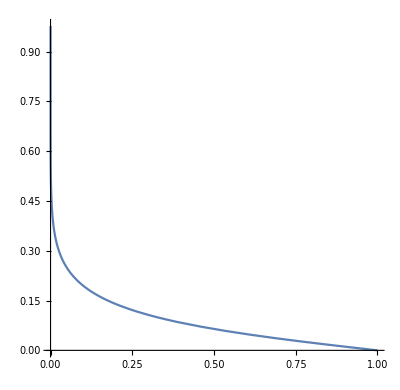

```mathematica
ParametricPlot[{A[d],B[d]},{d,0,5}]
```

```mathematica
(Integrate[1/2*Exp[-x/2],{x,0,3}])^2
```

```mathematica
N[(1-1/ⅇ^(3/2))^2]
```

0.603527

```mathematica
Integrate[Integrate[Exp[-x/2],{x,0,0.2-t}]*1/4*Exp[-1/2*t],{t,0,0.2}]
```

```mathematica
N[(1-1/ⅇ^(3/2))^2]-0.004678840160444467
```

0.598848

```mathematica
NIntegrate[1/Sqrt[t1*t2*t3*t4*t5],{t5,0,q-t1-t2-t3-t4}]
```

```mathematica
Integrate[2*Sqrt[q-t1-t2-t3-t4]/Sqrt[t4],{t4,0,q-t1-t2-t3}]
```

ConditionalExpression[π (q-t1-t2-t3),t1+t2+t3<Re[q]&&Im[q]==0]

```mathematica
Integrate[π (q-t1-t2-t3)/Sqrt[t3],{t3,0,q-t1-t2}]
```

4/3 π (q-t1-t2)^(3/2)

```mathematica
Integrate[4/3 π (q-t1-t2)^(3/2)/Sqrt[t2],{t2,0,q-t1}]
```

ConditionalExpression[1/2 π^2 (q-t1)^2,Re[q]>t1&&q==Re[q]]

```mathematica
Integrate[1/2 π^2 (q-t1)^2/Sqrt[t1],{t1,0,q}]
```

8/15 π^2 q^(5/2)

```mathematica
(15/8*0.06/Pi^2)^(2/5)
```

0.167009

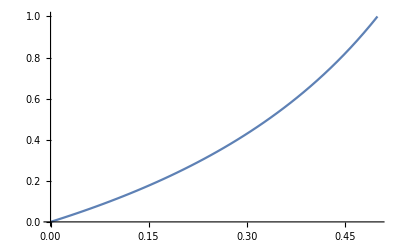

```mathematica
Plot[p/(1-p),{p,0,0.5}]
```

```mathematica
Limit[p/(1-p),p->0]
```

0